## version 79_binary

```mathematica
data=Import["/Users/wanglong/task/Nb6Test/79_binary_time.1","Table"][[6;;]];
label=Import["/Users/wanglong/task/Nb6Test/79_label","Table"][[1]];
plabel={"100k Singles+5k Binaries, 1NB Time unit, in Milkyway","500k Singles+25k Binaries, 1NB Time unit, in Milkyway","100k Singles, 1NB Time unit, in Milkyway","500k Singles, 1NB Time unit, in Milkyway"}[[2]];
```

```mathematica
TabView[Table[label[[j]]->ListLogLogPlot[data[[All,{1,j}]],PlotMarkers->Automatic,PlotRange->All,ImageSize->400,Joined->True,Epilog->First@LogLogPlot[data[[-1,j]]/x,{x,1,32},PlotStyle->Dotted],AxesLabel->label[[{1,j}]]],{j,3,Length@label,1}]]
```

12345678910111213141516171819202122232425

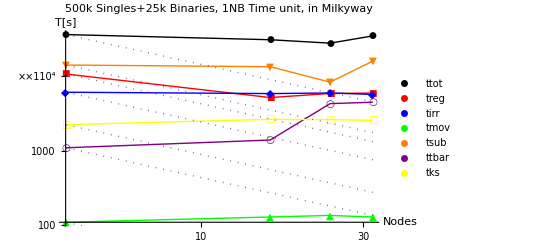

```mathematica
plotdata={Table[{data[[i,1]],(data[[i,3]]-data[[i,4]])},{i,Length@data}],data[[All,{1,6}]],data[[All,{1,7}]],data[[All,{1,11}]],
Table[{data[[i,1]],(data[[i,12]]+data[[i,13]])},{i,Length@data}],data[[All,{1,23}]],data[[All,{1,14}]]
};
plottitle=label[[{3,6,7,11,12,23,14}]];
plotcolor={Black,Red,Blue,Green,Orange,Purple,Yellow};
ListLogLogPlot[plotdata,PlotRange->Full,Joined->True,PlotStyle->plotcolor,PlotMarkers->Automatic,PlotLegends->plottitle,AxesLabel->{"Nodes","T[s]"},Epilog->First@LogLogPlot[Table[4*plotdata[[i,1,2]]/x,{i,Length@plotdata}],{x,1,64},PlotStyle->Dotted],ImageSize->400,PlotLabel->plabel]
```

## 256k

```mathematica
data=Import["/Users/wanglong/task/Nb6Test/milkynew/time.2","Table"];
label=Import["/Users/wanglong/task/Nb6Test/milkynew/label","Table"][[1]];
```

```mathematica
TabView[Table[label[[j]]->ListLogLogPlot[data[[All,{1,j}]],PlotMarkers->Automatic,PlotRange->All,ImageSize->400,Joined->True,Epilog->First@LogLogPlot[data[[-1,j]]/x,{x,1,32},PlotStyle->Dotted],AxesLabel->label[[{1,j}]]],{j,3,Length@label,1}]]
```

1234567891011121314151617181920212223

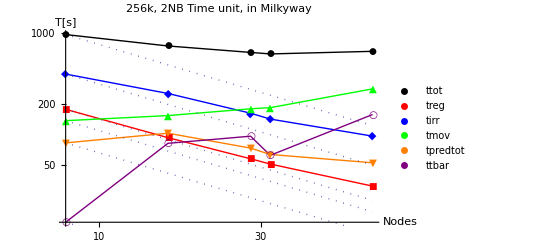

```mathematica
plotdata={Table[{data[[i,1]],(data[[i,3]]-data[[i,8]])},{i,Length@data}],data[[All,{1,4}]],data[[All,{1,5}]],data[[All,{1,12}]],
Table[{data[[i,1]],data[[i,6]]+data[[i,22]]},{i,Length@data}],data[[All,{1,20}]]
};
plottitle=label[[{3,4,5,12,6,20}]];
plotcolor={Black,Red,Blue,Green,Orange,Purple};
ListLogLogPlot[plotdata,PlotRange->Full,Joined->True,PlotStyle->plotcolor,PlotMarkers->Automatic,PlotLegends->plottitle,AxesLabel->{"Nodes","T[s]"},Epilog->First@LogLogPlot[Table[8*plotdata[[i,1,2]]/x,{i,Length@plotdata}],{x,1,64},PlotStyle->Dotted],ImageSize->400,PlotLabel->"256k, 2NB Time unit, in Milkyway"]
```

## Pie

```mathematica
timepie[pdata_,label_,title_,range_]:=
PieChart[pdata[[range]],ChartLabels->label[[range]],(*ChartLegends->label[[range]],*)PlotLabel->title,ImageSize->350]
```

```mathematica
new1m=Import["/Users/wanglong/task/Nb6Test/milkynew/1m32","Table"];
new8=Import["/Users/wanglong/task/Nb6Test/milkynew/8i","Table"];
new1m16=Import["/Users/wanglong/task/Nb6Test/milkynew/1m16","Table"];
label={new8[[1]],new1m16[[1]],new1m[[1]]};
plotdata={new8[[4]]-new8[[3]],new1m16[[3]]-new1m16[[2]],new1m[[4]]-new1m[[3]]};
plottitle={"256k, 8NP","1M, 16NP","1M, 32NP"};
Grid[{Table[timepie[plotdata[[i]],label[[i]],Style[plottitle[[i]]~~", T_Tot="~~ToString[plotdata[[i,3]]]~~"s",Large],{6,22,21,8,9,10,11,12,13,14,15,23}],{i,3}],Table[timepie[plotdata[[i]],label[[i]],Style[plottitle[[i]]~~", T_Tot="~~ToString[plotdata[[i,3]]-plotdata[[i,23]]]~~"s",Large],{6,22,21,8,9,10,11,12,13,14,15}],{i,3}]},Alignment->{{Right,Center,Left},{Bottom,Top}}]
```

-Graphics-

```mathematica
Clear[plottitle]
```